## MODELAGEM DA DINÂMICA PLANA DE AERONAVE SUPERSÔNICA DE PASSAGEIROS DURANTE FASE DE FREE-ROLL DA ATERRISSAGEM

## PME3380 - Modelagem de Sistemas Dinâmicos Prof. Dr. Agenor de Toledo Fleury Prof. Dr. Renato Maia Matarazzo Orsino

## Grupo K Lucas Retore Carboni - 12676091 Roberto Tetsuo Hamaoka - 10334770 Vitor Lucas Buter - 12555700

## Modelo principal - toque e free-roll

O equacionamento é baseado no seguinte modelo físico:
-Graphics-

e  são definidos como variáveis incrementais a partir da posição de equilíbrio dinâmico do avião transladando em pista plana com velocidade constante (M.R.U)
Importando as funções necessárias ao código

```mathematica
SetDirectory @ NotebookDirectory[];
<<Linearize.m
```

As coordenadas generalizadas são definidas como:

```mathematica
𝕢[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t]};
𝕧[t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]}; 
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = { Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, 𝕧[t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
α = 𝕢[t][[3]] + Subscript[Φ, 0];
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, PO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor P-O*)
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, GO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor G-O*)
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
D[Subscript[H, o], t] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[𝕧[t][[1]], t]) + Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(𝕢[t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + m*g //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) - Subscript[L, ext][[2]] + M*g //FullSimplify;
```

### O espaço de estados

```mathematica
DIN = {Subscript[TMB, m], Subscript[TMB, M], TQMA};

Sol[t_] = Flatten @ Solve[
	(# == 0)& /@ DIN,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;

𝕩[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
F = (𝕩'[t] /.Sol[t]); 
F //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(-g m+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(-2 M Cos[Φ_0+θ[t]] D_GO^2 (2 g M Cos[Φ_0+θ[t]]+Sin[Φ_0+θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol)+M D_GO (S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2-4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2)+2 J_oz (-S ρ C_L (u_longit+u_vento)^2+2 (g M+k_t (-q_1[t]+q_2[t])+c_t (-q_1'[t]+q_2'[t]))))/(4 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(Sec[Φ_0+θ[t]] (-S ρ C_D D_PO (u_longit+u_vento)^2 Tan[Φ_0+θ[t]]+S ρ C_L (u_longit+u_vento)^2 (-D_PO+D_GO (1+μ_rol Tan[Φ_0+θ[t]]))+2 D_GO (-g M μ_rol Tan[Φ_0+θ[t]]+k_t (q_1[t]-q_2[t])+M Sin[Φ_0+θ[t]] D_GO θ'[t]^2+c_t (q_1'[t]-q_2'[t]))))/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz))

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
Subscript[m, eq]= Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + m*g;
Subscript[M, eq] = Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[L, ext][[2]] + M*g;
Subscript[q, 1eq] = SolveValues[Subscript[m, eq] == 0/.(Subscript[q, 2][t] -> SolveValues[Subscript[M, eq] == 0, 𝕢[t][[2]]]), 𝕢[t][[1]]];
Subscript[q, 2eq] = SolveValues[Subscript[M, eq] == 0/.(Subscript[q, 1][t] -> SolveValues[Subscript[m, eq] == 0, 𝕢[t][[1]]]), 𝕢[t][[2]]];
```

```mathematica
POSequi = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINlin = Linearize[DIN, POSequi]; (*ELS -> Equação dinâmica não-linear*)

Sollin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINlin,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
	
Subscript[𝕩, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[F, lin] = (Subscript[𝕩, lin]'[t] /.Sollin[t]);
Subscript[F, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(-g m+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M Cos[Φ_0] D_GO^2 ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+M S ρ Cos[Φ_0] D_GO D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))+J_oz (-S ρ C_L (u_longit+u_vento)^2+2 (g M+k_t (-q_1[t]+q_2[t])+c_t (-q_1'[t]+q_2'[t]))))/(2 M (M Cos[Φ_0]^2 D_GO^2-J_oz))
(-S ρ C_D D_PO (u_longit+u_vento)^2 (Sin[Φ_0]+Cos[Φ_0] θ[t])+S ρ C_L (u_longit+u_vento)^2 (D_PO (-Cos[Φ_0]+Sin[Φ_0] θ[t])+D_GO (Cos[Φ_0]+μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])))-2 D_GO (g M Sin[Φ_0] (μ_rol+θ[t])+Cos[Φ_0] (g M μ_rol θ[t]+k_t (-q_1[t]+q_2[t])+c_t (-q_1'[t]+q_2'[t]))))/(2 M Cos[Φ_0]^2 D_GO^2-2 J_oz))

```mathematica
𝔸 = CoefficientArrays[Subscript[F, lin], Subscript[𝕩, lin][t]][[2]]//Normal; 
𝔸 //FullSimplify//MatrixForm;

𝔹 = CoefficientArrays[Subscript[F, lin], 𝕦[t]][[2]]//Normal; 
𝔹 //MatrixForm;

ℂ = { {0,1,0,0,0,0}, {0,0,1,0,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}};
ℂ //MatrixForm;

𝔻 = {{0,0},{0,0},{0,0},{0,0}};
𝔻 //MatrixForm;

𝕩[t] //MatrixForm ;
𝕩'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
𝔸.𝕩[t] //MatrixForm;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> (27.66^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->11*Pi/180)/.(Subscript[u, longit]->80)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹/.(rep)/.(Subscript[Φ, 0]->11*Pi/180)/.(Subscript[u, longit]->80)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻}]
```

000100000000100000000100-125434/1557434/150-13987/37525549/750013600/397/30133.788-133.788-0.1848641.19029-1.19029000-1.507641.507640.0856017-0.01341320.013413200001000000001000000000100000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2461FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TF = TransferFunctionModel[SS, s]
```

(606504.+5395.96 s)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)(432.58+3.84859 s)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)-(60.8064 (-9.57262×10^-13+2.05662×10^-14 s+112.4 s^2+s^3))/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)-(0.0433693 (-1.31068×10^-12 s+112.4 s^2+s^3))/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)(606504. s+5395.96 s^2)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)(432.58 s+3.84859 s^2)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)(-6834.62 s^3-60.8064 s^4)/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)(-4.87469 s^3-0.0433693 s^4)/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.1506786201432.5801662929589-60.80639254364632-0.04336926526957541606504.15067862432.5801662928398-6834.620433973584-4.874692515408241606486.7302364681606486.7302364684-50654.31375934252-50654.31375934252606486.7505692882606486.7505692885-50654.31375934252-50654.313759342521FalseFalseFalseAutomaticNoneAutomatic

```mathematica
(606504.1506786201+5395.958681508539 s)/(606486.7302364681+5828.46114724859 s+8499.900851941247 s^2+38.48895166994061 s^3+s^4)(432.5801662929589+3.848588177252168 s)/(606486.7302364684+5828.461147248592 s+8499.900851941247 s^2+38.48895166994061 s^3+s^4)-(60.80639254364632 (-9.572621969258648*^-13+2.0566180012079127*^-14 s+112.39970253238857 s^2+s^3))/(-50654.31375934252-486.7907914969778 s+605776.8312530449 s^2+5825.246607674605 s^3+8499.817333439587 s^4+38.48895166994061 s^5+s^6)-(0.04336926526957541 (-1.3106843869150132*^-12 s+112.39970253250722 s^2+s^3))/(-50654.31375934252-486.7907914969778 s+605776.8312530449 s^2+5825.246607674605 s^3+8499.817333439587 s^4+38.48895166994061 s^5+s^6)(606504.15067862 s+5395.958681508537 s^2)/(606486.7505692882+5828.461239318044 s+8499.90085433335 s^2+38.48895166994061 s^3+s^4)(432.5801662928398 s+3.848588177252168 s^2)/(606486.7505692885+5828.461239318047 s+8499.90085433335 s^2+38.48895166994061 s^3+s^4)(-6834.620433973584 s^3-60.806392543647235 s^4)/(-50654.31375934252-486.7907914969778 s+605776.8312530449 s^2+5825.246607674605 s^3+8499.817333439587 s^4+38.48895166994061 s^5+s^6)(-4.874692515408241 s^3-0.04336926526957541 s^4)/(-50654.31375934252-486.7907914969778 s+605776.8312530449 s^2+5825.246607674605 s^3+8499.817333439587 s^4+38.48895166994061 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.1506786201432.5801662929589-60.80639254364632-0.04336926526957541606504.15067862432.5801662928398-6834.620433973584-4.874692515408241606486.7302364681606486.7302364684-50654.31375934252-50654.31375934252606486.7505692882606486.7505692885-50654.31375934252-50654.313759342521FalseFalseFalseAutomaticNoneAutomatic
```

(606504.+5395.96 s)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)(432.58+3.84859 s)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)-(60.8064 (-9.57262×10^-13+2.05662×10^-14 s+112.4 s^2+s^3))/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)-(0.0433693 (-1.31068×10^-12 s+112.4 s^2+s^3))/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)(606504. s+5395.96 s^2)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)(432.58 s+3.84859 s^2)/(606487.+5828.46 s+8499.9 s^2+38.489 s^3+s^4)(-6834.62 s^3-60.8064 s^4)/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)(-4.87469 s^3-0.0433693 s^4)/(-50654.3-486.791 s+605777. s^2+5825.25 s^3+8499.82 s^4+38.489 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.1506786201432.5801662929589-60.80639254364632-0.04336926526957541606504.15067862432.5801662928398-6834.620433973584-4.874692515408241606486.7302364681606486.7302364684-50654.31375934252-50654.31375934252606486.7505692882606486.7505692885-50654.31375934252-50654.313759342521FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TF] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TF] [[4]][[1]] //MatrixForm
```

(-19.0614-89.7247 ⅈ
-19.0614+89.7247 ⅈ
-0.183061-8.48813 ⅈ
-0.183061+8.48813 ⅈ)

(-19.0614-89.7247 ⅈ
-19.0614+89.7247 ⅈ
-0.289
-0.183061-8.48813 ⅈ
-0.183061+8.48813 ⅈ
0.289)

```mathematica
TransferFunctionZeros[TF]
```

{{{-112.4},{-112.4}},{{-112.4,-9.22854×10^-8,9.22854×10^-8},{-112.4,0,1.16609×10^-14}},{{-112.4,0},{-112.4,0}},{{-112.4,0,0,0},{-112.4,0,0,0}}}

### Diagrama de Bode

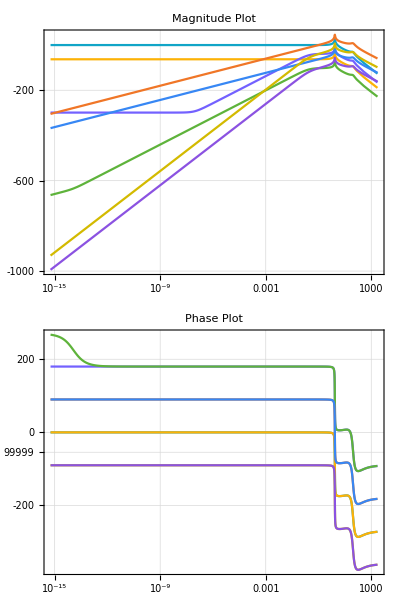

```mathematica
BodePlot[TF, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Pós toque

### Modelo incluindo trem de pouso frontal

-Graphics-

```mathematica
Subscript[𝕢, T][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t]};
Subscript[𝕧, T][t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = {Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, Subscript[𝕧, T][t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(Subscript[𝕢, T][t][[3]])], Subscript[D, PO]*Sin[(Subscript[𝕢, T][t][[3]])], 0} (*Vetor P-O*);
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(Subscript[𝕢, T][t][[3]])], Subscript[D, GO]*Sin[(Subscript[𝕢, T][t][[3]])], 0} (*Vetor G-O*);
Subscript[ρ, FO] = {Subscript[D, FO]*Cos[(Subscript[𝕢, T][t][[3]])], Subscript[D, FO]*Sin[(Subscript[𝕢, T][t][[3]])], 0} (*Vetor G-O*);
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[F, f] = {0, -Subscript[k, Tf]*(Subscript[D, FO]*Sin[θ[t]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]) - Subscript[c, Tf]*(D[(Subscript[D, FO]*Sin[θ[t]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]), t]), 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, Tf] = Cross[Subscript[ρ, FO], Subscript[F, f]] //FullSimplify;
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso] - Subscript[M, Tf])[[3]]//FullSimplify
```

-1/2 S ρ (Sin[θ[t]] C_D+Cos[θ[t]] C_L) D_PO (u_longit+u_vento)^2+Cos[θ[t]] D_FO^2 (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+Cos[θ[t]] D_FO (k_Tf (q_2[t]-q_3[t])+c_Tf (q_2'[t]-q_3'[t]))+J_oz θ''[t]+1/2 D_GO (Sin[θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol+2 M Cos[θ[t]] (g+q_2''[t]))

### Aplicação do TMB no conjunto do trem de pouso (m e mf) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[Subscript[𝕧, T][t][[1]], t]) + Subscript[k, r]*(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]) - Subscript[c, t]*(D[(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]), t]) + m*g //FullSimplify;
Subscript[TMB, mf] = Subscript[m, f]*(D[Subscript[𝕧, T][t][[4]], t]) + Subscript[k, rf]*(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]) + Subscript[c, rf]*(D[(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]), t]) - Subscript[k, Tf]*(Subscript[D, FO]*Sin[θ[t]] + Subscript[q, 2][t] - Subscript[q, 3][t]) - Subscript[c, Tf]*(D[(Subscript[D, FO]*Sin[θ[t]]+ Subscript[q, 2][t] - Subscript[q, 3][t]), t]) + Subscript[m, f]*g //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + Subscript[k, Tf]*(Subscript[D, FO]*Sin[θ[t]] + Subscript[q, 2][t] - Subscript[q, 3][t]) + Subscript[c, Tf]*(D[(Subscript[D, FO]*Sin[θ[t]]+ Subscript[q, 2][t] - Subscript[q, 3][t]), t]) - Subscript[L, ext][[2]] + M*g //FullSimplify;
```

### O espaço de estados

```mathematica
DINf = {Subscript[TMB, m], Subscript[TMB, M], TQMA, Subscript[TMB, mf]};

Solf[t_] = Flatten @ Solve[
	(# == 0)& /@ DINf,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
𝕩f[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Ff = (𝕩f'[t] /.Solf[t]); 
Ff //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(-g m+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M Cos[θ[t]] D_GO^2 (-2 g M Cos[θ[t]]+Sin[θ[t]] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+2 (g M+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))+M D_GO (S ρ Cos[θ[t]] (Sin[θ[t]] C_D+Cos[θ[t]] C_L) D_PO (u_longit+u_vento)^2-2 Sin[θ[t]] J_oz θ'[t]^2-2 Cos[θ[t]]^2 D_FO^2 (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+2 Cos[θ[t]]^2 D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(2 M (M Cos[θ[t]]^2 D_GO^2-J_oz))
(S ρ Sec[θ[t]] C_L (u_longit+u_vento)^2 (-D_PO+D_GO (1+μ_rol Tan[θ[t]]))+2 D_FO^2 (k_Tf Tan[θ[t]]+c_Tf θ'[t])-Sec[θ[t]] (S ρ C_D D_PO (u_longit+u_vento)^2 Tan[θ[t]]+2 D_GO (g M μ_rol Tan[θ[t]]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])-M Sin[θ[t]] D_GO θ'[t]^2+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))-2 Sec[θ[t]] D_FO (k_Tf (-q_2[t]+q_3[t])+D_GO (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+c_Tf (-q_2'[t]+q_3'[t])))/(2 M D_GO^2-2 Sec[θ[t]]^2 J_oz)
(-g m_f+k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
(*Subscript[m, eq]= Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + m*g;
Subscript[M, eq] = Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[L, ext][[2]] + M*g;
Subscript[q, 1eq] = SolveValues[Subscript[m, eq] == 0/.(Subscript[q, 2][t] -> SolveValues[Subscript[M, eq] == 0, 𝕢[t][[2]]]), 𝕢[t][[1]]];
Subscript[q, 2eq] = SolveValues[Subscript[M, eq] == 0/.(Subscript[q, 1][t] -> SolveValues[Subscript[m, eq] == 0, 𝕢[t][[1]]]), 𝕢[t][[2]]];*)
```

```mathematica
POSequif = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0, Subscript[q, T1][t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINflin = Linearize[DINf, POSequif]; (*ELS -> Equação dinâmica não-linear*)

Solflin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINflin,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
Subscript[𝕩f, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], Subscript[θ, T][t], Subscript[q, T1][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], Subscript[θ, T]'[t], Subscript[q, T1]'[t]};
Subscript[Ff, lin] = (Subscript[𝕩f, lin]'[t] /.Solflin[t]);
Subscript[Ff, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ_T'[t]
q_T1'[t]
(-g m+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-2 g M+(2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol θ_T[t])+J_oz (-S ρ C_L (u_longit+u_vento)^2+2 (g M+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_T1[t]+D_FO θ_T[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_T1'[t])+c_Tf D_FO θ_T'[t]))+M D_GO (S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ_T[t])-2 D_FO (k_Tf (q_2[t]-q_T1[t]+D_FO θ_T[t])+c_Tf (q_2'[t]-q_T1'[t]+D_FO θ_T'[t]))))/(2 M (M D_GO^2-J_oz))
(2 D_FO k_Tf q_2[t]-2 D_FO k_Tf q_T1[t]+2 D_FO^2 k_Tf θ_T[t]-S ρ C_D D_PO u_longit^2 θ_T[t]-2 S ρ C_D D_PO u_longit u_vento θ_T[t]-S ρ C_D D_PO u_vento^2 θ_T[t]+S ρ C_L (u_longit+u_vento)^2 (-D_PO+D_GO (1+μ_rol θ_T[t]))+2 c_Tf D_FO q_2'[t]-2 c_Tf D_FO q_T1'[t]+2 c_Tf D_FO^2 θ_T'[t]-2 D_GO (k_t (-q_1[t]+q_2[t])+g M μ_rol θ_T[t]+k_Tf (q_2[t]-q_T1[t]+D_FO θ_T[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_T1'[t])+c_Tf D_FO θ_T'[t]))/(2 M D_GO^2-2 J_oz)
(-g m_f+k_rf (-q_T1[t]+y_ext[t])+k_Tf (q_2[t]-q_T1[t]+D_FO θ_T[t])+c_rf (-q_T1'[t]+y_ext'[t])+c_Tf (q_2'[t]-q_T1'[t]+D_FO θ_T'[t]))/m_f)

```mathematica
𝔸f = CoefficientArrays[Subscript[Ff, lin], Subscript[𝕩f, lin][t]][[2]]//Normal; 
𝔸f //FullSimplify//MatrixForm;

𝔹f = CoefficientArrays[Subscript[Ff, lin], 𝕦[t]][[2]]//Normal; 
𝔹f //MatrixForm;

ℂf = { {0,1,0,0,0,0,0,0}, {0,0,1,0,0,0,0,0}, {0,0,0,0,0,1,0,0}, {0,0,0,0,0,0,1,0}};
ℂf //MatrixForm;

𝔻f = {{0,0},{0,0},{0,0},{0,0}};
𝔻f //MatrixForm;
 
𝕩f[t] //MatrixForm ;
𝕩f'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.15714, Subscript[C, L] -> 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, Subscript[k, Tf] -> 5743400, Subscript[c, Tf] -> 51098, Subscript[k, rf]-> 3400000, Subscript[c, rf] -> 2425, m -> 3000, Subscript[m, f] -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, Subscript[D, FO] -> 32.5, ρ -> 1.2923, S -> (27.66^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂf, 𝔻f}]
```

0000100000000001000000000010000000000100-125434/1557434/1500-13987/37525549/7500013600/397/30133.914-175.89-1364.4141.97581.19141-1.56486-12.13720.37345100-1.5373-9.04913-343.9710.5864-0.0136771-0.0805085-3.061030.094185600028717/1562220.2-15239/5025549/1500553.562-17841/10003400/397/1200100000000001000000000000100000000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TFf = TransferFunctionModel[SS, s]
```

(2.47278×10^11+4.57723×10^9 s+2.4891×10^9 s^2+3.6505×10^7 s^3+784081. s^4+5824.29 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(1.76367×10^8+3.26464×10^6 s+1.77531×10^6 s^2+26036.7 s^3+559.234 s^4+4.15409 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(0.000152588+2.86102×10^-6 s+7.40502×10^7 s^2+937148. s^3+7505.16 s^4+44.7407 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(0.000244141+1.90735×10^-6 s+52815.2 s^2+668.407 s^3+5.35294 s^4+0.0319107 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(2.47278×10^11 s+4.57723×10^9 s^2+2.4891×10^9 s^3+3.6505×10^7 s^4+784081. s^5+5824.29 s^6)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(1.76367×10^8 s+3.26464×10^6 s^2+1.77531×10^6 s^3+26036.7 s^4+559.234 s^5+4.15409 s^6)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(44.7407 (1.27893×10^-7 s+4.26311×10^-8 s^2+1.65509×10^6 s^3+20946.2 s^4+167.748 s^5+s^6))/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(0.0319107 (0.000119543 s+0.0000597715 s^2+1.65509×10^6 s^3+20946.2 s^4+167.748 s^5+s^6))/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s242.4727788206165613e111.763673129409485e80.0001525878906250.0002441406252.4727788206165616e111.7636731294103432e844.740744373893910.03191067797160942.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
(2.4727788206165613*^11+4.5772317052035055*^9 s+2.489099566429406*^9 s^2+3.6505010114922896*^7 s^3+784080.6890311239 s^4+5824.293089650164 s^5)/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(1.763673129409485*^8+3.2646432015037537*^6 s+1.7753136613502502*^6 s^2+26036.66162608564 s^3+559.2340208552778 s^4+4.154091394855641 s^5)/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(0.000152587890625+2.86102294921875*^-6 s+7.405017750272846*^7 s^2+937147.6916018277 s^3+7505.1566459573805 s^4+44.74074437387753 s^5)/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(0.000244140625+1.9073486328125*^-6 s+52815.20013046265 s^2+668.4068094491959 s^3+5.352942608296871 s^4+0.031910677964333445 s^5)/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(2.4727788206165616*^11 s+4.577231705203507*^9 s^2+2.4890995664294066*^9 s^3+3.650501011492288*^7 s^4+784080.6890311239 s^5+5824.29308965016 s^6)/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(1.7636731294103432*^8 s+3.264643201505661*^6 s^2+1.7753136613503692*^6 s^3+26036.66162608564 s^4+559.2340208530659 s^5+4.154091394822899 s^6)/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(44.74074437389391 (1.2789339959610278*^-7 s+4.2631133198700925*^-8 s^2+1.6550948925636976*^6 s^3+20946.180147790623 s^4+167.74769286882028 s^5+s^6))/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)(0.0319106779716094 (0.00011954297144732859 s+0.000059771485723664293 s^2+1.655094892613394*^6 s^3+20946.18014834628 s^4+167.74769287369762 s^5+s^6))/(2.47277882061656*^11+4.753599018144536*^9 s+5.805324233818615*^9 s^2+8.514580407316835*^7 s^3+3.053538048319894*^7 s^4+323087.29022980883 s^5+12755.170346382056 s^6+59.765556890373546 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s242.4727788206165613e111.763673129409485e80.0001525878906250.0002441406252.4727788206165616e111.7636731294103432e844.740744373893910.03191067797160942.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e111FalseFalseFalseAutomaticNoneAutomatic
```

(2.47278×10^11+4.57723×10^9 s+2.4891×10^9 s^2+3.6505×10^7 s^3+784081. s^4+5824.29 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(1.76367×10^8+3.26464×10^6 s+1.77531×10^6 s^2+26036.7 s^3+559.234 s^4+4.15409 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(0.000152588+2.86102×10^-6 s+7.40502×10^7 s^2+937148. s^3+7505.16 s^4+44.7407 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(0.000244141+1.90735×10^-6 s+52815.2 s^2+668.407 s^3+5.35294 s^4+0.0319107 s^5)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(2.47278×10^11 s+4.57723×10^9 s^2+2.4891×10^9 s^3+3.6505×10^7 s^4+784081. s^5+5824.29 s^6)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(1.76367×10^8 s+3.26464×10^6 s^2+1.77531×10^6 s^3+26036.7 s^4+559.234 s^5+4.15409 s^6)/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(44.7407 (1.27893×10^-7 s+4.26311×10^-8 s^2+1.65509×10^6 s^3+20946.2 s^4+167.748 s^5+s^6))/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)(0.0319107 (0.000119543 s+0.0000597715 s^2+1.65509×10^6 s^3+20946.2 s^4+167.748 s^5+s^6))/(2.47278×10^11+4.7536×10^9 s+5.80532×10^9 s^2+8.51458×10^7 s^3+3.05354×10^7 s^4+323087. s^5+12755.2 s^6+59.7656 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s242.4727788206165613e111.763673129409485e80.0001525878906250.0002441406252.4727788206165616e111.7636731294103432e844.740744373893910.03191067797160942.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e112.47277882061656e111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TFf] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TFf] [[4]][[1]] //MatrixForm
```

(-19.0643-89.7248 ⅈ
-19.0643+89.7248 ⅈ
-10.4196-56.4486 ⅈ
-10.4196+56.4486 ⅈ
-0.243641-11.8836 ⅈ
-0.243641+11.8836 ⅈ
-0.15526-7.94401 ⅈ
-0.15526+7.94401 ⅈ)

(-19.0643-89.7248 ⅈ
-19.0643+89.7248 ⅈ
-10.4196-56.4486 ⅈ
-10.4196+56.4486 ⅈ
-0.243641-11.8836 ⅈ
-0.243641+11.8836 ⅈ
-0.15526-7.94401 ⅈ
-0.15526+7.94401 ⅈ)

```mathematica
TransferFunctionZeros[TFf]
```

{{{-112.4,-10.9234-59.4903 ⅈ,-10.9234+59.4903 ⅈ,-0.188017-10.1594 ⅈ,-0.188017+10.1594 ⅈ},{-112.4,-10.9234-59.4903 ⅈ,-10.9234+59.4903 ⅈ,-0.188017-10.1594 ⅈ,-0.188017+10.1594 ⅈ}},{{-112.4,-27.674-118.149 ⅈ,-27.674+118.149 ⅈ,-6.27909×10^-15-1.43548×10^-6 ⅈ,-6.27909×10^-15+1.43548×10^-6 ⅈ},{-112.4,-27.674-118.149 ⅈ,-27.674+118.149 ⅈ,1.11937×10^-11-0.0000679893 ⅈ,1.11937×10^-11+0.0000679893 ⅈ}},{{-112.4,-10.9234-59.4903 ⅈ,-10.9234+59.4903 ⅈ,-0.188017-10.1594 ⅈ,-0.188017+10.1594 ⅈ,0},{-112.4,-10.9234-59.4903 ⅈ,-10.9234+59.4903 ⅈ,-0.188017-10.1594 ⅈ,-0.188017+10.1594 ⅈ,0}},{{-112.4,-27.674-118.149 ⅈ,-27.674+118.149 ⅈ,-1.23898×10^-14-2.77979×10^-7 ⅈ,-1.23898×10^-14+2.77979×10^-7 ⅈ,0},{-112.4,-27.674-118.149 ⅈ,-27.674+118.149 ⅈ,-1.75998×10^-11-8.49866×10^-6 ⅈ,-1.75998×10^-11+8.49866×10^-6 ⅈ,0}}}

### Diagrama de Bode

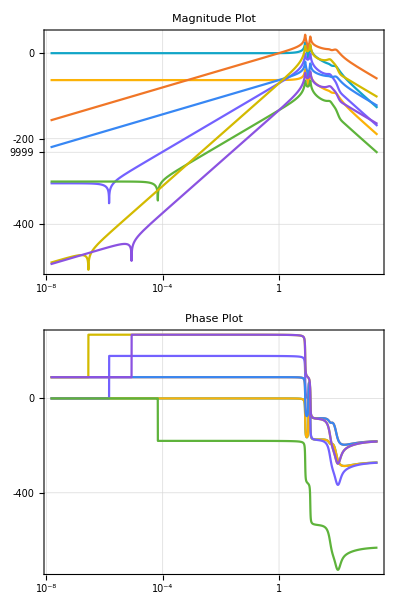

```mathematica
BodePlot[TFf, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Exportando o aquivo .m do espaço de estados

Para exportar outro espaço de estados, basta substituir o argumento da 4 linha da terceira célula de código por:
WriteString[fileD, (#/.(({ii_}→vv_):>(StringReplace[StringReplace[ToString @ StringForm[“    ``;”, (vv /. crule //CForm)], csqrule], csorule]<>”\n”)))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩’[t]/.NOMEDASOLUCAO[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};
```

```mathematica
fileD = OpenWrite["trab_esp_postoque.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩f'[t]/.Solf[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```